```mathematica
getPara[a_,b_,h_]:=Function[x,(-4 h)/(a-b)^2*(x-a)(x-b)];
```

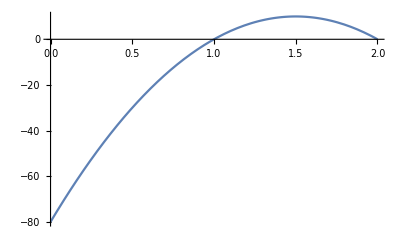

```mathematica
Plot[getPara[1,2,10][x],{x,0,2}]
```

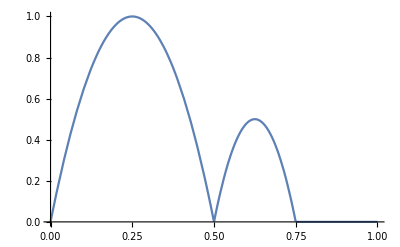

```mathematica
getDoublePara[a_,b_,h_]:=(
p1=getPara[0,a,h];
p2=getPara[a,b,h/2];
Function[x,Piecewise[{{p1[x],x<a},{p2[x], x<b} },0]]
)
Plot[getDoublePara[1/2,3/4,1][x],{x,0,1}]
```

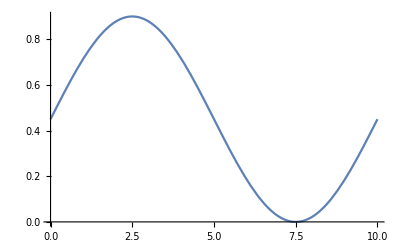

```mathematica
getSine[T_,a_,b_]:=Function[x,a+(Sin[(2π)/T x]+1)/2(b-a)];
Plot[getSine[10,0,0.9][x],{x,0,10}]
```